## Monte Carlo Methods Case Study

We got pretty far into Monte Carlo theory in the three “Why Do They Work?” write-ups:

* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-I.nb.pdf
* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-II.nb.pdf
* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-III.nb.pdf

We also got pretty far when we were studying Bayesian conjugates. Now we are going to put all of these ideas together in a case study. The case study is the Hepatitis B vaccination study described in Chapter 2 of Markov Chain Monte Carlo in Practice, by Gilks, Richardson, and Spiegelhalter. Gilks, Richardson, and Spiegelhalter are the editors. Chapter 2’s authors are Spiegelhalter, Best, Gilks, and Inskip.

## The Likelihoods and the Priors

On pp. 27 and 28 of Chapter 2, Spiegelhalter, Best, Gilks, and Inskip describe the likelihoods and the priors for analyzing the Hepatitis B data. Before I show you any math, I want to show you a diagram from p. 26 of that chapter. (I am going to show you the same diagram again after doing the math.)

-Graphics-

You can find diagrams like these in Chapter 19 of Donovan and Mickey. You don’t need to go look there. I am hoping this case study makes it clear how the diagrams work.

Let’s look at just a few things in the diagram for starters. At the bottom of the digram is a number σ. That is the standard deviation of the errors in the blood samples, y_(i,j). The cool thing about this analysis is that σ is not going to be given. It is going to be distributed according to a prior.

As a second thing in the diagram is the α_i and the β_i. Those are the intercept and slope of the linear fits to the titers, which is a fancy name for a blood test that measures antibodies to Hepatitis B. They aren’t going to be a best fit using the frequentist methods we studied months ago. They are controlled by the parameters above them, which are in turn controlled by priors.

Let’s dive in to the actual math, and then the diagram above and the words that go along with it are likely to be more meaningful.

### The Likelihoods for the y_(i,j)

On p. 27 the likelihoods for the y_(i,j), the α_i, and the β_i are given by these four equations:

-Graphics-

Let’s focus on the y_(i,j)’s. The first two equations say that the likelihood for the y_(i,j)’s is:

P_y=1/(√(2π)σ)^(∑_j n_j)e^(-∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2 σ^2)     where     v_(i,j)≡log(t_(i,j))/730

The babies are indexed by i, where i=1,..., n, and n=106. The blood samples for a given baby are indexed by j where j=1,..., n_j. Also, ∑_(i,j) is a compact way of writing ∑_i ∑_j which is a “double sum.”

If it wasn’t at all obvious that that was what the first two equations say, that is because the authors are using a compact notation used by statisticians which we have not introduced in our class. The ~ means “statistically distributed according to,” and the N(μ,σ^2) means “a Gaussian with mean μ and variance σ^2.” If it helps you remember what the equations mean, I’ll mention that statisticians use N because they usually refer to Gaussian distributions as “normal distributions.”

Putting all the verbiage together, the first two equations say, “the y_(i,j) are statistically distributed normally around the μ_(i,j) with variance σ^2 and the μ_(i,j) are  linear functions of log of the t_(i,j).”

I did one other thing to make my equation prettier, which was to define the v_(i,j) so logarithms and the number of days in two years (365·2=730) don’t cause clutter. It makes it more obvious that it is just a linear fit with a bit of preprocessing of the times.

### If There Were Only One Baby in the Study

If the number of indices is obscuring my equation, let’s drop from 106 babies to only 1 baby. Then we wouldn’t need the index i or the sum on i. We’d just have:

P_y=1/(√(2π)σ)^n_j e^(-∑_j (y_j-α_1-β_1 v_j)^2/2 σ^2)     where     v_j≡log t_j/730

Is it perhaps more obvious that this is a likelihood if I mention that  this is exactly the same function we maximized (by minimizing  ∑_j (y_j-α_1-β_1 v_j)^2) when we did the frequentist derivation of linear regression all the way back on Sept. 27? Anyway, we actually have 106 babies, and so we have to reintroduce i, and the ∑_i  in the exponential just means the total likelihood is the product of the likelihoods for all the babies.

### The Likelihoods for the α_i and the β_i

The third equation from p. 27 says the likelihood for the α_i’s are:

P_α=1/(√(2π)σ_α)^i e^(-∑_i (α_i-α_0)^2/2 σ_α^2)

The fourth equation says the likelihood for the β_i’s are:

P_β=1/(√(2π)σ_β)^i e^(-∑_i (β_i-β_0)^2/2 σ_β^2)

### The Priors

You will notice that five new parameters have appeared in these equations: σ^2, α_0, σ_α^2, β_0 and σ_β^2. These are called “parent parameters.” We aren’t going to just assume values for the parent parameters. We need priors for them. On p. 28 of Chapter 2, the priors are given in these two equations:

-Graphics-

Now 10,000 is just some really big number. In fact, it is the square of 100. Let me define w=100. Then the first equation  from p. 28 says that the priors for α_0 and β_0 are normally distributed as follows:

P_α_0=1/(√(2π)w)e^(-α_0^2/2 w^2)

P_β_0=1/(√(2π)w)e^(-β_0^2/2 w^2)

The Ga in the second equation refers to the Gamma distribution. The inverses, σ^-2, σ_α^-2, and σ_β^-2  in the second equation are telling us that we should define some new variables

τ=1/σ^2, τ_α=1/σ_α^2, and τ_β=1/σ_β^2

and then the priors for τ, τ_α, and τ_β are Gamma distributed. Let me define u=0.01. Then we would write this gamma distributions as:

P_τ=u^u/(Γ(u))τ^(u-1)e^-uτ

P_τ_α=u^v/(Γ(u))τ_α^(u-1)e^(-u τ_α)

P_τ_β=u^u/(Γ(u))τ_β^(u-1)e^(-u τ_β)

So we have a total of five priors, one for each parameter, and the complete prior is the product of all five priors.

The reason they used w=100 and u=0.01 is that they were trying for very uninformative priors. I used w because in my mind it stood for “wide.”

You might remember that the way you make a beta distribution extra uninformative is to make it very U-shaped by choosing α and β to be small. That was in Donovan and Mickey Chapter 10. In Chapter 11 on p. 159, they defined g(x;α,β)=β^α/(Γ(α))x^(α-1)e^-βx.

All that is going on in an equation like P_τ=u^u/(Γ(u))τ^(u-1)e^-uτ is that α=β=u=0.01 and u is so small to make the gamma distribution uninformative.

In fact, before we leave these priors, let me show you just how uninformative they are trying to be:

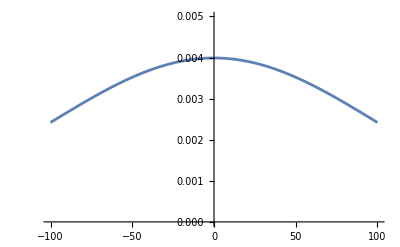

```mathematica
Plot[1/(√(2Pi) w)Exp[-Subscript[α, o]^2/(2 w^2)]/.w->100,{Subscript[α, o],-100, 100}, PlotRange->{{-100,100},{0,0.005}}]
```

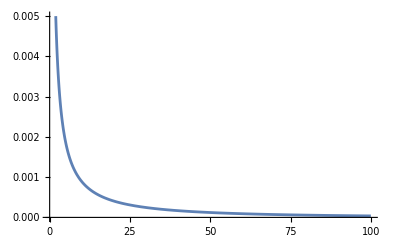

```mathematica
Plot[u^u/Gamma[u] t^(u-1)Exp[-u*t]/.u->0.01,{t,0, 100}, PlotRange->{{0,100},{0,0.005}}]
```

## The Posterior

Well the posterior is the high-dimensional function going to try to sample using Gibbs sampling. It is the product of the three likelihood equations and the five prior equations above:

P(τ,α_0,τ_α,β_(0,)τ_β,{α_i},{β_i})=P_y P_α P_β·P_α_0 P_β_0 P_τ P_τ_α P_τ_β/denominator=
      1/(√(2π/τ))^(∑_j n_j)e^(-τ∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2)·1/(√(2π/τ_α))^ne^(-τ_α∑_i (α_i-α_0)^2/2)·1/(√(2π/τ_β))^ne^(-τ_β∑_i (β_i-β_0)^2/2)·
                1/(√(2π)w)e^(-α_0^2/2 w^2)·1/(√(2π)w)e^(-β_0^2/2 w^2)·u^u/(Γ(u))τ^(u-1)e^-uτ·u^u/(Γ(u))τ_α^(u-1)e^(-u τ_α)·u^u/(Γ(u))τ_β^(u-1)e^(-u τ_β)

                ÷ denominator (the most horrible denominator with 217 integrals)

This is our posterior function of 217 parameters. I can’t even look at this function in the above form and see what it means. Let’s rewrite it by stripping out every last one of the constant factors:

P(τ,α_0,τ_α,β_(0,)τ_β,{α_i},{β_i})∝τ^(u-1+∑_j n_j/2)e^(-τ∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2)e^-uτ·
τ_α^(u-1+n/2)e^(-τ_α∑_i (α_i-α_0)^2/2)e^(-u τ_α)·
τ_β^(u-1+n/2)e^(-τ_β∑_i (β_i-β_0)^2/2)e^(-u τ_β)
	   e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)

Notice that in ignoring the constants, I definitely am not allowed to get rid of all the powers of τ, τ_α, and τ_β. Those are not constants.

Possibly it helps to remember how factorials factor. Rewrite:

e^(-τ∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2)=∏_i e^(-τ∑_j (y_(i,j)-α_i-β_i v_(i,j))^2/2)

And rewrite:

e^(-τ_α∑_i (α_i-α_0)^2/2)=∏_i e^(-(τ_α(α_i-α_0))^2/2)

And rewrite:

e^(-τ_β∑_i (β_i-β_0)^2/2)=∏_i e^(-(τ_β(β_i-β_0))^2/2)

Then,

P(τ,α_0,τ_α,β_(0,)τ_β,{α_i},{β_i})∝τ^(u-1+∑_j n_j/2)∏_i e^(-τ∑_j (y_(i,j)-α_i-β_i v_(i,j))^2/2)e^-uτ·
τ_α^(u-1+n/2)∏_i e^(-(τ_α(α_i-α_0))^2/2)e^(-u τ_α)·
τ_β^(u-1+n/2)∏_i e^(-(τ_β(β_i-β_0))^2/2)e^(-u τ_β)·
e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)

### The Power of Factorization for the α_i Axis

We have the factorization we said we were going to get in the last of three “Why Do They Work?” write-ups. The factorization means that whenever we move in one of the 217 directions, only a very few of the factors above change. As an example, let’s imagine that α_i is changing (for just one of the i's) and that every other parameter stays constant. Then P(t,α_0,t_α,β_(0,)t_β,{α_i},{β_i}) can be thought of as:

P(α_i)∝e^(-τ∑_j (y_(i,j)-α_i-β_i v_(i,j))^2/2)·e^(-(τ_α(α_i-α_0))^2/2)

What is the coefficient of α_i^2 in the exponential? It is -(τ+n_i τ_α)/2 where n_i is the number of titers for baby i. So the variance is

1/(τ+n_i τ_α)

By completing the square, you can find the mean of this Gaussian. It is

(τ_α α_0+τ∑_j (y_(i,j)-β_i v_(i,j)))/(τ+n_i τ_α)

All we have said is something that we didn’t do much with back in Chapter 12, because I thought it was too much math for our course, but it boiled down to “the likelihood that is conjugate to a Gaussian prior is another Gaussian distribution.” Meaning that when you take the product of a Gaussian prior with a Gaussian likelihood you get a Gaussian posterior, just with new parameters.

Of course, we know how to normalize and sample Gaussians! Even when they have messy coefficients. So what we have shown is that when the Gibbs sampling algorithm needs to move along the α_i axis in this 217-dimensional posterior, it just has to sample from this new and messy, but 1-dimensional Gaussian distribution.

The above formulas can be found on p. 30 of Chapter 2.

### The Power of Factorization for the τ Axis

It would be a good exercise to do another axis and show that what happened on the α_i axis wasn’t a fluke. Every axis has a simple interpretation. For example, we could go along the τ axis. Then the only factors that depend on τ are:

P(τ)∝τ^(u-1+∑_j n_j/2)∏_i e^(-τ∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2)e^-uτ

This is just another gamma distribution! The prior had a gamma distributed τ, and then we multiplied it by a likelihood involving the data and τ, and we get another gamma distribution. Remembering that gamma distributions look like

g(τ;α,β)∝τ^(α-1)e^-βτ

We need to compare and discover what the new α and β are. Doing that comparison, we get that

α=u+∑_j n_j/2

and

β=-u+∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2

So when the Gibbs sampling algorithm needs to move along the τ axis, it just has to sample from this new and messy but one-dimensional gamma distribution.

### The Power of Factorization for the τ_α Axis

As one more axis to consider as an example, we could go along the τ_α axis. Then the only factors that depend on τ_α are:

P(τ_α)∝τ_α^(u-1+n/2)e^(-∑_i (τ_α(α_i-α_0))^2/2)e^(-u τ_α)

This is yet another gamma distribution! The prior had a gamma distributed τ, and then we multiplied it by a likelihood involving the data and τ, and we get another gamma distribution. Just as with the τ axis, we need to do a comparison. This time with:

g(τ_α;α,β)∝τ_α^(α-1)e^(-β τ_α)

Again, we need to compare and discover what the new α and β are.

Doing that comparison, we get that

α=u+n/2

and

β=-u+∑_i (α_i-α_0)^2/2

So when the Gibbs sampling algorithm needs to move along the τ_α axis, it just has to sample from yet another new and messy but one-dimensional gamma distribution.

These formulas can be found on p. 31 of Chapter 2.

## The Conclusion

You would still have to write a lot of code to sample along each axis with Gibbs sampling if only because the means, variances, alphas, and betas are messy. Maybe that is why it took until 1994 for the BUGS program to mature and be published.

However, moving one axis at a time has for every parameter become a one-dimensional and tractable problem involving distributions we are already completely familiar with: namely Gaussian distributions and gamma distributions.

That means we can get a representative distribution out of this 217-dimensional space using Gibbs sampling. Using these representative samples, we can inquire about the most important results from the Hepatitis B data. The parameter we are most interested in would be α_0. Remember that roughly-speaking, α_0 controls the mean of the α_i via the likelihood function,

P_α=1/(√(2π)σ_α)^n e^(-∑_i (α_i-α_0)^2/2 σ_α^2)

and the α_i represent the rate of increase of the Hepatitis B titers. We would also be interested in the variance of the α_i and that roughly speaking can be found by examining t_α=σ_α^-2. However, we don’t want to know the typical values of these things in the prior. We want to know what they central values and their ranges are in the posterior.

The posterior was described by an very complex function, so complex it helped to have a graphic to interpret it:

-Graphics-

You now know what every bubble in this diagram refers to.

The goal of looking closely at this case study is to see how the posterior can be practically sampled using Gibbs sampling, such as with the BUGS program.

The reference for the BUGS program is Gilks, Thomas, and Spiegelhalter, “A language and program for complex Bayesian modelling,” The Statistician, 43 (1994) 169-177, but I haven’t ever used the program or studied the original reference. I learned this stuff from Donovan and Mickey and Chapters 1 and 2 of Spiegelhalter, Best, Gilks, and Inskip.